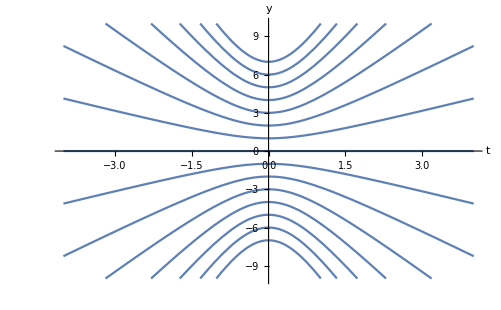
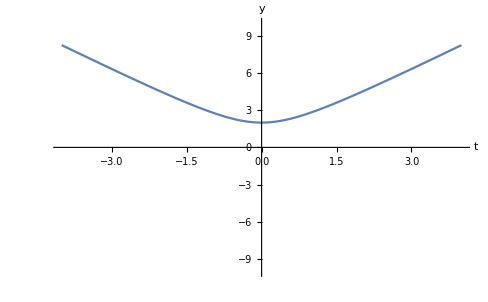
Equazione inziale: y'=t/(t^2+1)y

solution=DSolve[y'[t]==t/(t^2+1)*y[t],y[t],t]

{{y[t]→√(1+t^2) C[1]}}

f[t_]=y[t]/.solution[[1]]
F[t_]=Table[f[t]/.C[1]->j,{j,-7,7}]
Plot[F[t],{t,-4,4},AxesLabel->{t,y},PlotRange->{-10,10}]

-Graphics-

Condizione data: y(0)=2

cauchy=DSolve[{y'[t]==t/(t^2+1)*y[t],y[0]==2},y[t],t]

{{y[t]→2 √(1+t^2)}}

g[t_]=y[t]/.cauchy[[1]]
Plot[g[t],{t,-4,4},AxesLabel->{t,y},PlotRange->{-10,10}]

-Graphics-